```mathematica
SetDirectory[NotebookDirectory[]];
```

## Bar

```mathematica
xMin=0.5;
xMax=4.2;
yMin=0;
yMax=0.2;
xMax2=xMax-xMin;
dx=0.1;
dy=0.5;
dy2=0.15;
dy3=0.22;
cfMAX[x_]:=ColorData["SunsetColors"][(x-0.1)/0.45];
barMAX=Graphics[{
{Raster[{Range[0.1,0.55,1/1000]},{{xMin,yMin},{xMax,yMax}},ColorFunction->cfMAX]},AbsoluteThickness[cm[0.02]],Line[{{xMin,yMin},{xMax,yMin},{xMax,yMax},{xMin,yMax},{xMin,yMin}}],
Line[{{xMin+0/3*xMax2,0},{xMin+0/3*xMax2,-dy2}}],
Line[{{xMin+1/3*xMax2,0},{xMin+1/3*xMax2,-dy2}}],
Line[{{xMin+2/3*xMax2,0},{xMin+2/3*xMax2,-dy2}}],
Line[{{xMin+3/3*xMax2,0},{xMin+3/3*xMax2,-dy2}}],
Line[{{xMin+1*xMax2,0},{xMin+1*xMax2,-dy2}}],
Inset[Style["0.1",FontFamily->"Helvetica",FontSize->7],{xMin+0/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.25",FontFamily->"Helvetica",FontSize->7],{xMin+1/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.4",FontFamily->"Helvetica",FontSize->7],{xMin+2/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.55",FontFamily->"Helvetica",FontSize->7],{xMin+3/3*xMax2,-dy3},{Center,Top}]




},PlotRange->{{0,xMax+xMin},{yMin-2*dy,yMax+dy}},ImageSize->cm[xMax+xMin],ImagePadding->0]
```

-Graphics-

## Fig A

```mathematica
maxAllList={};
indMAX[p1_,p2_,probCL_,pd_]:=(
fileName="diversity_prob1_"<>ToString[p1]<>"_prob2_"<>ToString[p2]<>"_prob_cl_"<>ToString[probCL]<>"_pd_"<>ToString[pd]<>"_.dat";
maxIN=Import["IND//output//diversity//"<>fileName,"Table"];
{p2,probCL,maxIN[[1001]][[16]]}
)
minMax[v_,x0_,x1_,y0_,y1_]:=(
{Min[Max[v[[1]],x0],x1],Min[Max[v[[2]],y0],y1]})
isSame[v1_,v2_]:=Total[Total[Abs[v1-v2]]]<0.0001
count2[xyz_,x_]:=(
cn=0;Do[If[isSame[xyz[[ii]],x],cn+=1],{ii,1,Length[xyz]}];
cn)
trueLines[linesIN_]:=(
linesOUT={};
Do[
If[count2[linesIN,linesIN[[jj]]]==1,AppendTo[linesOUT,linesIN[[jj]]]],{jj,1,Length[linesIN]}];
linesOUT)
```

```mathematica
p2List={1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10};
probList={0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1};
maxOutList={};

linesExperiment={};

(*x distance between points*)
dx=0.5;

(*y distance between points*)
dy0=0.05;
dy1=0.05;

size=3*6/5;

(*smallest and largest values in x,y direction*)
xMIN=1;
xMAX=10;
yMIN=0;
yMAX=1;

Do[
Do[
GG=indMAX[1,p2List[[i]],probList[[j]],0.026];
AppendTo[maxOutList,GG];
AppendTo[maxAllList,GG[[3]]];

If[Abs[GG[[3]]-0.36]<0.06,

x0=GG[[1]];
y0=GG[[2]];

dy=dy0;

(*add four lines surrounding the coordinate if withing standard deviation of experiment*)
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0+dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0+dy/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0+dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0+dy/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0-dx/2,y0+dy/2},xMIN,xMAX,yMIN,yMAX]
}];

];
,{j,1,Length[probList]}],{i,1,Length[p2List]}]
```

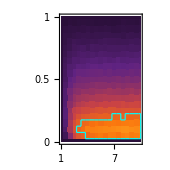

```mathematica
b=ListDensityPlot[maxOutList,ColorFunction->cfMAX,ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->{{xMIN,xMAX},{yMIN,yMAX},{0.1,0.55}}];


(*Lines around experimentally comparable values*)
lineColor=Cyan;
lineTh=0.03;

linesplot=ListLinePlot[trueLines[linesExperiment],PlotRange->{
{xMIN,xMAX},{yMIN,yMAX}},PlotStyle->{{lineColor,AbsoluteThickness[cm[lineTh]]}},AspectRatio->1];
fLegend=5;
FigA=plotBack[
{b,linesplot},
xTicks->{1,4,7,10},
yTicks->{0,0.25,0.5,0.75,1},
tickLength->0.12,
plotRange->{{xMIN,xMAX},{yMIN,yMAX}},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{1.2,0.6,1.2,1.2},
plotLabels->{
Row[{Style["Division weight ratio "],Subscript[Style["w",Italic],Style["f",FontSize->5]],Style["/"],Subscript[Style["w",Italic],Style["s",FontSize->5]]}],
Row[{Style["Fast cluster probability "],Subscript[Style["p",Italic],Style["f",FontSize->5]]}]},
labelsDistance->{0.55,0.8},
plotTitle->True,
titleText->Row[{Style["Independent (Largest fraction)"]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
```

## Fig B

```mathematica
cctMAX[t1_,sig1_,t12_,sig2_,prob_,pd_]:=(
fileName="diversity_t1_"<>ToString[t1]<>"_sig1_"<>ToString[sig1]<>"_t0r_"<>ToString[t12]<>"_sig2_"<>ToString[sig2]<>"_prob_"<>ToString[prob]<>"_pd_"<>ToString[pd]<>"_.dat";
maxIN=Import["CCT//output//diversity//"<>fileName,"Table"];
{t12,prob,maxIN[[1001]][[16]]}
)
```

```mathematica
cctPlot[sigS_,sigF_]:=(
p2List={0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1};
probList={0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1};
maxOutList={};

linesExperiment={};

(*x distance between points*)
dx=0.05;

(*y distance between points*)
dy0=0.05;

size=3*6/5;

(*smallest and largest values in x,y direction*)
xMIN=0.05;
xMAX=1;
yMIN=0;
yMAX=1;

Do[
Do[
GG=cctMAX[9.6,sigS,p2List[[i]],sigF,probList[[j]],0.026];
AppendTo[maxOutList,GG];
AppendTo[maxAllList,GG[[3]]];

If[Abs[GG[[3]]-0.36]<0.06,

x0=GG[[1]];
y0=GG[[2]];

dy=dy0;

(*add four lines surrounding the coordinate if withing standard deviation of experiment*)
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0+dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0+dy/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0+dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0+dy/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0-dx/2,y0+dy/2},xMIN,xMAX,yMIN,yMAX]
}];

];
,{j,1,Length[probList]}],{i,1,Length[p2List]}];
b=ListDensityPlot[maxOutList,ColorFunction->cfMAX,ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->{{xMIN,xMAX},{yMIN,yMAX},{0.1,0.55}}];


(*Lines around experimentally comparable values*)
lineColor=Cyan;
lineTh=0.03;

linesplot=ListLinePlot[trueLines[linesExperiment],PlotRange->{
{xMIN,xMAX},{yMIN,yMAX}},PlotStyle->{{lineColor,AbsoluteThickness[cm[lineTh]]}},AspectRatio->1];
fLegend=5;
plotBack[
{b,linesplot},
xTicks->{0,0.25,0.5,0.75,1},
yTicks->{0,0.25,0.5,0.75,1},
tickLength->0.12,
plotRange->{{xMIN,xMAX},{yMIN,yMAX}},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{1.2,0.6,1.2,1.2},
plotLabels->{
Row[{Style["Mean division time ratio "],Subscript[Style["t",Italic],Style["f",FontSize->5]],Style["/"],Subscript[Style["t",Italic],Style["s",FontSize->5]]}],
Row[{Style["Fast cluster probability "],Subscript[Style["p",Italic],Style["f",FontSize->5]]}]},
labelsDistance->{0.55,0.8},
plotTitle->True,
titleText->Row[{Style["Cell Cycle (Largest fraction)"]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)
```

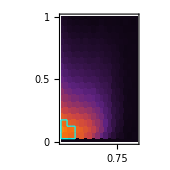

```mathematica
FigB=cctPlot[0.5,0.5]
```

```mathematica
Max[maxAllList]
```

0.361648

```mathematica
Min[maxAllList]
```

0.109561

## Figure

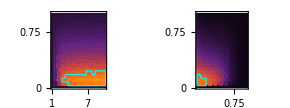

```mathematica
tMAX=Row[{Style["Largest cluster fractional size",FontFamily->"Arial",FontSize->7]}];
dX=5;
dY=-5;
dY2=-1.2;

FigED8=figure[10.25,6.9,
elements->{tMAX,barMAX,FigA,FigB},
elementCoordinates->{
{0.5*dX+1.2+3*6/5/2,-0.6},
{0.5*dX+1.2+3*6/5/2,-1.3},

{0*dX,0*dY+dY2-0.5},
{1*dX,0*dY+dY2-0.5}
},
centeredElements->{1,2}]
```

```mathematica
Export["figs//SYS_ED_Fig8.pdf",FigED8]
```

figs//SYS_ED_Fig8.pdf